```mathematica
P1:={{Cos[ϕ]^2,Cos[ϕ]*Sin[ϕ]},{Cos[ϕ]*Sin[ϕ],Sin[ϕ]^2}}
P2:={{Sin[ϕ]^2,-Cos[ϕ]*Sin[ϕ]},{-Cos[ϕ]*Sin[ϕ],Cos[ϕ]^2}}
```

```mathematica
MatrixForm[P1]
MatrixForm[P2]
```

(Cos[ϕ]^2 | Cos[ϕ] Sin[ϕ]
Cos[ϕ] Sin[ϕ] | Sin[ϕ]^2)

(Sin[ϕ]^2 | -Cos[ϕ] Sin[ϕ]
-Cos[ϕ] Sin[ϕ] | Cos[ϕ]^2)

```mathematica
V1:={{Cos[θ]},{Sin[θ]}}
V2:={{Cos[θ]},{-Sin[θ]}}
```

```mathematica
Dot[Transpose[V1],P2,V1]
Dot[Transpose[V2],P1,V2]
```

{{Sin[θ] (Cos[ϕ]^2 Sin[θ]-Cos[θ] Cos[ϕ] Sin[ϕ])+Cos[θ] (-Cos[ϕ] Sin[θ] Sin[ϕ]+Cos[θ] Sin[ϕ]^2)}}

{{Cos[θ] (Cos[θ] Cos[ϕ]^2-Cos[ϕ] Sin[θ] Sin[ϕ])-Sin[θ] (Cos[θ] Cos[ϕ] Sin[ϕ]-Sin[θ] Sin[ϕ]^2)}}

```mathematica
p12=Simplify[Dot[Transpose[V2],P1,V2]]
p21=Simplify[Dot[Transpose[V1],P2,V1]]
p11=Simplify[Dot[Transpose[V1],P1,V1]]
p22=Simplify[Dot[Transpose[V2],P2,V2]]
```

{{Cos[θ+ϕ]^2}}

{{Sin[θ-ϕ]^2}}

{{Cos[θ-ϕ]^2}}

{{Sin[θ+ϕ]^2}}

### Demo Sergis

```mathematica
Simplify[(Sin[a]*Sin[b]+Cos[a]*Cos[b])^2]
Simplify[(Sin[a]*Sin[b]-Cos[a]*Cos[b])^2]
Simplify[(Cos[a]*Sin[b]-Sin[a]*Cos[b])^2]
Simplify[(Cos[a]*Sin[b]+Sin[a]*Cos[b])^2]
```

Cos[a-b]^2

Cos[a+b]^2

Sin[a-b]^2

Sin[a+b]^2

## Calculs guarros

```mathematica
D[Pe,t]
Reduce[D[Pe,t]==0,t]
```

0

True

```mathematica
Reduce[(Cos[t+f]Sin[t+f]+Sin[t-f]Cos[t-f])==0,f]
```

((C[1]|C[2])∈Integers&&((t==1/2 (-π-4 π C[2])&&f==π+2 π C[1])||(t==-2 π C[2]&&f==π+2 π C[1])||(t==1/2 (π-4 π C[2])&&f==π+2 π C[1])||(t==-π-2 π C[2]&&f==π+2 π C[1])))||(C[1]∈Integers&&(((-π-t)/(2 π)∉Integers&&(f==-2 ArcTan[1+√2]+2 π C[1]||f==2 ArcTan[1-√2]+2 π C[1]||f==-2 ArcTan[1-√2]+2 π C[1]||f==2 ArcTan[1+√2]+2 π C[1]))||((f-π)/(2 π)∉Integers&&(t==π/2-2 π C[1]||t==-2 π C[1]||t==-π/2-2 π C[1]||t==-π-2 π C[1]))))

```mathematica
N[2 ArcTan[1+√2]]
```

2.35619

```mathematica
N[Pi/4+Pi/2]
```

2.35619

```mathematica
Dot[Transpose[V1],V2]
Simplify[Abs[Dot[Transpose[V1],V2]]]
```

{{Cos[θ]^2-Sin[θ]^2}}

{{Abs[Cos[2 θ]]}}

```mathematica
1/2Simplify[p1+p2]
1/2TrigReduce[p1+p2]
```

{{1/2 (1-4 Cos[t] Cos[θ] Sin[t] Sin[θ])}}

{{1/4 (2-Cos[2 t-2 θ]+Cos[2 t+2 θ])}}

```mathematica
TrigExpand[-Cos[ a- b]+Cos[ a+b]]
```

-2 Sin[a] Sin[b]

```mathematica
Simplify[1/4 (2-2 Cos[2θ] Cos[2ϕ])]
```

1/2 (1-Cos[2 θ] Cos[2 ϕ])

## Apartat 2

```mathematica
Dynamic[Plot[{Cos[t-Pi/4]^(2*n1),Cos[t+Pi/4]^(2*n1)},{t,0,2Pi},PlotRange->All]]
{Slider[Dynamic[n1],{0,1000,25}],Dynamic[n1]}
```

{,}

```mathematica
PEs=Simplify[Sin[θ-ϕ]^2+ Cos[θ+ϕ]^2]
PSs=Simplify[Sin[θ+ϕ]^2+ Cos[θ-ϕ]^2]
```

1-4 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]

1+Sin[2 θ] Sin[2 ϕ]

## Apartat 3

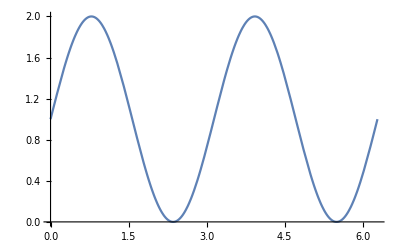

```mathematica
Plot[1+ Sin[2 ϕ],{ϕ,0,2Pi}]
```

```mathematica
Sin[2(Pi/4+Pi)]
```

1